```mathematica
DSolve[f'[x]==ϵ^((-I Pi)/6)3Log[1/(f[x]*)], f, x]
```

{{f→Function[{x},InverseFunction[1/Log[1/Conjugate[K[1]]]K[1]1#1&][3 x ϵ^(-(ⅈ π)/6)+C[1]]]}}

```mathematica
DSolve[f'[x]==3Log[1/f[x]], f, x]
```

{{f→Function[{x},InverseFunction[-ExpIntegralEi[-Log[1/#1]]&][3 x+C[1]]]}}

```mathematica
upperB:=-9.94
sol=NDSolve[{f'[x]Sin[f[x]]==3f[x], f[-10]==2Pi/3}, f, {x, -10, upperB}]
```

{{f→InterpolatingFunction[…]}}

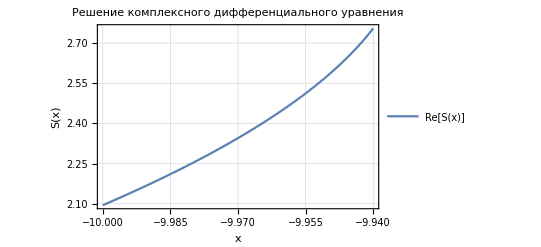

```mathematica
Plot[Evaluate[f[x]/.sol],{x,-10,upperB},PlotLegends->{"Re[S(x)]","Im[S(x)]"},PlotLabel->"Решение комплексного дифференциального уравнения",Frame->True,GridLines->Automatic,AxesLabel->{"x","S(x)"}]
```

```mathematica
solInv=NDSolve[{z'[θ]==-Sin[θ]/θ, z[0.01]==100000}, z,{θ, 0, 20Pi}]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

NDSolve::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {θ,z[θ]} = {0.,100000.}.

{{z→InterpolatingFunction[…]}}

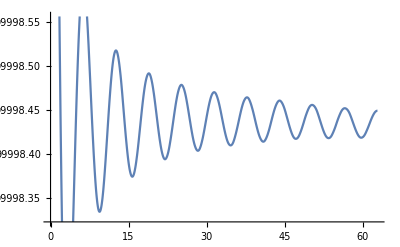

```mathematica
Plot[Evaluate[z[θ]/.solInv],{θ,0,20Pi}]
```

NDSolve::ndsz: At x == -7.744, step size is effectively zero; singularity or stiff system suspected.

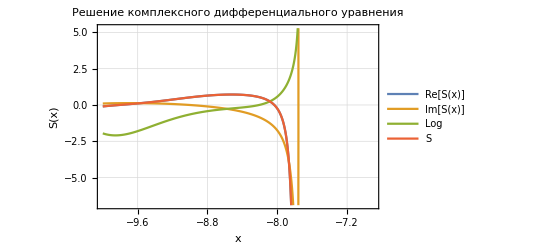

```mathematica
a=1;x0=-10;xmax=-6.9;S0=-0.1+0.1I;eqn=S'[x]==-3Exp[(-I π)/6 ] Abs[S[x]]^(4/3)Log[(S[x]*)/a];

(*Численное решение*)
sol=NDSolve[{eqn,S[x0]==S0},S,{x,x0,xmax}];

(*Построение графиков*)
Plot[{Evaluate[ReIm[S[x]/. sol]],Evaluate[Re[Log[(S[x]*)/a]/.sol]], Evaluate[Re[S[x]/.sol]]},{x,x0,xmax},PlotLegends->{"Re[S(x)]","Im[S(x)]", "Log", "S"},PlotLabel->"Решение комплексного дифференциального уравнения",Frame->True,GridLines->Automatic,AxesLabel->{"x","S(x)"}]
```

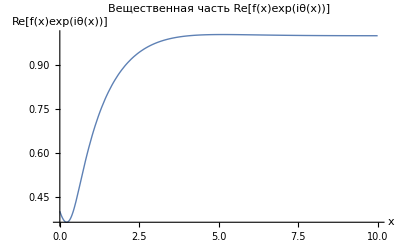

```mathematica
x0:=0
xmax:=10
xmin:=-10
solRight=NDSolve[{f'[x]Cos[θ[x]]-f[x]*θ'[x]Sin[θ[x]]==-Log[Abs[f[x]]]Cos[-Pi/6]+θ[x]Sin[-Pi/6], f'[x]Sin[θ[x]]+f[x]*θ'[x]Cos[θ[x]]==-Log[Abs[f[x]]]Sin[-Pi/6]-θ[x]Cos[-Pi/6],f[0]==0.8,(*Начальное условие для f(x)*)θ[0]==Pi/3                  (*Начальное условие для θ(x)*)},{f,θ},{x,x0,xmax}];(*Диапазон по x*)(*Вычисляем вещественную часть*)realPart[x_]:=Re[f[x] Exp[I θ[x]]/. {solRight[[1]][[1]], solRight[[1]][[2]]}];
(*Строим график вещественной части*)Plot[realPart[x],{x,x0,xmax},PlotLabel->"Вещественная часть Re[f(x)exp(iθ(x))]",AxesLabel->{"x","Re[f(x)exp(iθ(x))]"},PlotStyle->Thick,PlotRange->All]
```

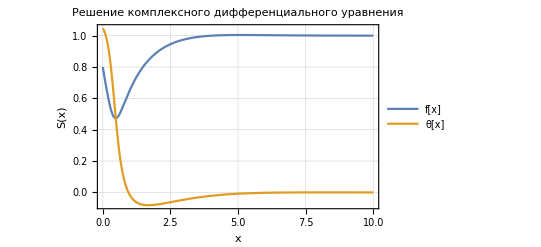

```mathematica
Plot[{Evaluate[f[x]/. solRight[[1]][[1]]], Evaluate[θ[x]/.solRight[[1]][[2]]]},{x,x0,xmax},PlotLegends->{"f[x]","θ[x]"},PlotLabel->"Решение комплексного дифференциального уравнения",Frame->True,GridLines->Automatic,AxesLabel->{"x","S(x)"}]
```

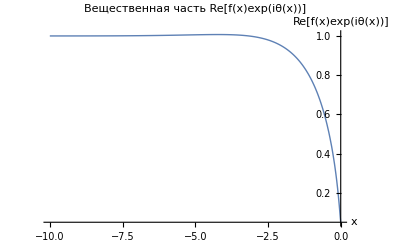

```mathematica
solLeft=NDSolve[{f'[x]Cos[θ[x]]-f[x]*θ'[x]Sin[θ[x]]==Log[Abs[f[x]]]Cos[-Pi/6]-θ[x]Sin[-Pi/6], f'[x]Sin[θ[x]]+f[x]*θ'[x]Cos[θ[x]]==Log[Abs[f[x]]]Sin[-Pi/6]+θ[x]Cos[-Pi/6],f[0]==0.1,(*Начальное условие для f(x)*)θ[0]==Pi/3                  (*Начальное условие для θ(x)*)},{f,θ},{x,xmin,x0}];(*Диапазон по x*)(*Вычисляем вещественную часть*)realPart[x_]:=Re[f[x] Exp[I θ[x]]/. {solLeft[[1]][[1]], solLeft[[1]][[2]]}];
(*Строим график вещественной части*)Plot[realPart[x],{x,xmin,x0},PlotLabel->"Вещественная часть Re[f(x)exp(iθ(x))]",AxesLabel->{"x","Re[f(x)exp(iθ(x))]"},PlotStyle->Thick,PlotRange->All]
```

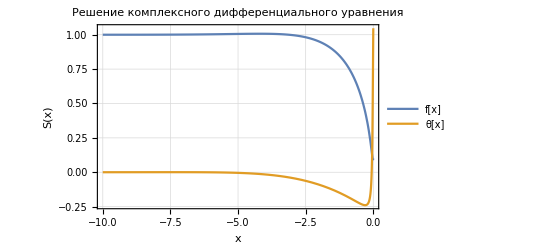

```mathematica
Plot[{Evaluate[f[x]/. solLeft[[1]][[1]]], Evaluate[θ[x]/.solLeft[[1]][[2]]]},{x,xmin,x0},PlotLegends->{"f[x]","θ[x]"},PlotLabel->"Решение комплексного дифференциального уравнения",Frame->True,GridLines->Automatic,AxesLabel->{"x","S(x)"}]
```